Лабораторная работа №3
Точки покоя линейной автономной системы

Piecewise[{{dx_1/dt, = -x_1+2 x_2}, {dx_2/dt, =x_1}}]

```mathematica
A={{-1,2},{1,0}};
```

Матрица системы:

```mathematica
A//MatrixForm
```

(-1 | 2
1 | 0)

```mathematica
Eigenvalues[A]
```

{-2,1}

```mathematica
Eigenvectors[A]
```

{{-2,1},{1,1}}

Точка покоя:

```mathematica
Solve[{-x1+2x2==0,x1==0}]
```

{{x1→0,x2→0}}

Характер точки покоя: седло, точка покоя неустойчива.

Решение задачи Коши методом Рунге - Кутты 4-го порядка:
1)

```mathematica
f[t_,x1_,x2_]:=-1*x1+2*x2;
g[t_,x1_,x2_]:=x1;
h=0.01;
a=-1;
b=1;
n=(b-a)/h;
t=a;
x1=-0.9;
x2=0.2;
tx1={{t,x1}};
tx2={{t,x2}};
tx1x2={{t,x1,x2}};
For[i=0,i<n,i++,
m1=h*f[t,x1,x2];
k1=h*g[t,x1,x2];
m2=h*f[t+h/2,x1+m1/2,x2+k1/2];
k2=h*g[t+h/2,x1+m1/2,x2+k1/2];
m3=h*f[t+h/2,x1+m2/2,x2+k2/2];
k3=h*g[t+h/2,x1+m2/2,x2+k2/2];
m4=h*f[t+h,x1+m3,x2+k3];
k4=h*g[t+h,x1+m3,x2+k3];
x1=x1+(m1+2m2+2m3+m4)/6;
x2=x2+(k1+2k2+2k3+k4)/6;
t=t+h;
tx1x2=Append[tx1x2,{t,x1,x2}];
tx1=Append[tx1,{t,x1}];
tx2=Append[tx2,{t,x2}]];
```

2)

```mathematica
t2=a;
x1=-0.4;
x2=0.4;
t2x1={{t2,x1}};
t2x2={{t2,x2}};
t2x1x2={{t2,x1,x2}};
For[i=0,i<n,i++,
m1=h*f[t2,x1,x2];
k1=h*g[t2,x1,x2];
m2=h*f[t2+h/2,x1+m1/2,x2+k1/2];
k2=h*g[t2+h/2,x1+m1/2,x2+k1/2];
m3=h*f[t2+h/2,x1+m2/2,x2+k2/2];
k3=h*g[t2+h/2,x1+m2/2,x2+k2/2];
m4=h*f[t2+h,x1+m3,x2+k3];
k4=h*g[t2+h,x1+m3,x2+k3];
x1=x1+(m1+2m2+2m3+m4)/6;
x2=x2+(k1+2k2+2k3+k4)/6;
t2=t2+h;
t2x1x2=Append[t2x1x2,{t2,x1,x2}];
t2x1=Append[t2x1,{t2,x1}];
t2x2=Append[t2x2,{t2,x2}]];
```

3)

```mathematica
t3=a;
x1=0.9;
x2=-0.2;
t3x1={{t3,x1}};
t3x2={{t3,x2}};
t3x1x2={{t3,x1,x2}};
For[i=0,i<n,i++,
m1=h*f[t3,x1,x2];
k1=h*g[t3,x1,x2];
m2=h*f[t3+h/2,x1+m1/2,x2+k1/2];
k2=h*g[t3+h/2,x1+m1/2,x2+k1/2];
m3=h*f[t3+h/2,x1+m2/2,x2+k2/2];
k3=h*g[t3+h/2,x1+m2/2,x2+k2/2];
m4=h*f[t3+h,x1+m3,x2+k3];
k4=h*g[t3+h,x1+m3,x2+k3];
x1=x1+(m1+2m2+2m3+m4)/6;
x2=x2+(k1+2k2+2k3+k4)/6;
t3=t3+h;
t3x1x2=Append[t3x1x2,{t3,x1,x2}];
t3x1=Append[t3x1,{t3,x1}];
t3x2=Append[t3x2,{t3,x2}]];
```

4)

```mathematica
t4=a;
x1=-0.5;
x2=0.5;
t4x1={{t4,x1}};
t4x2={{t4,x2}};
t4x1x2={{t4,x1,x2}};
For[i=0,i<n,i++,
m1=h*f[t4,x1,x2];
k1=h*g[t4,x1,x2];
m2=h*f[t4+h/2,x1+m1/2,x2+k1/2];
k2=h*g[t4+h/2,x1+m1/2,x2+k1/2];
m3=h*f[t4+h/2,x1+m2/2,x2+k2/2];
k3=h*g[t4+h/2,x1+m2/2,x2+k2/2];
m4=h*f[t4+h,x1+m3,x2+k3];
k4=h*g[t4+h,x1+m3,x2+k3];
x1=x1+(m1+2m2+2m3+m4)/6;
x2=x2+(k1+2k2+2k3+k4)/6;
t4=t4+h;
t4x1x2=Append[t4x1x2,{t4,x1,x2}];
t4x1=Append[t4x1,{t4,x1}];
t4x2=Append[t4x2,{t4,x2}]];
```

5)

```mathematica
t5=a;
x1=0.7;
x2=-0.5;
t5x1={{t5,x1}};
t5x2={{t5,x2}};
t5x1x2={{t5,x1,x2}};
For[i=0,i<n,i++,
m1=h*f[t5,x1,x2];
k1=h*g[t5,x1,x2];
m2=h*f[t5+h/2,x1+m1/2,x2+k1/2];
k2=h*g[t5+h/2,x1+m1/2,x2+k1/2];
m3=h*f[t5+h/2,x1+m2/2,x2+k2/2];
k3=h*g[t5+h/2,x1+m2/2,x2+k2/2];
m4=h*f[t5+h,x1+m3,x2+k3];
k4=h*g[t5+h,x1+m3,x2+k3];
x1=x1+(m1+2m2+2m3+m4)/6;
x2=x2+(k1+2k2+2k3+k4)/6;
t5=t5+h;
t5x1x2=Append[t5x1x2,{t5,x1,x2}];
t5x1=Append[t5x1,{t5,x1}];
t5x2=Append[t5x2,{t5,x2}]];
```

Сепаратисы седла прямолинейные: х2 =  x1 , x2=-x1

InterpolatingFunction::dmval: Input value {-2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

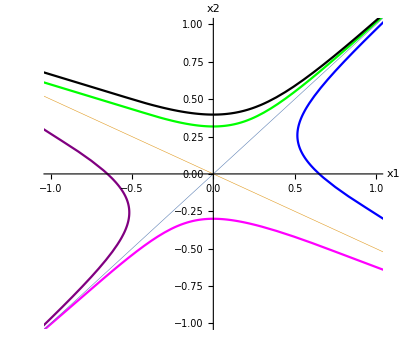

```mathematica
{sol1,sol2}={Interpolation[tx1,InterpolationOrder->1],Interpolation[tx2,InterpolationOrder->1]};
{sol3,sol4}={Interpolation[t2x1,InterpolationOrder->1],Interpolation[t2x2,InterpolationOrder->1]};
{sol5,sol6}={Interpolation[t3x1,InterpolationOrder->1],Interpolation[t3x2,InterpolationOrder->1]};
{sol7,sol8}={Interpolation[t4x1,InterpolationOrder->1],Interpolation[t4x2,InterpolationOrder->1]};
{sol9,sol10}={Interpolation[t5x1,InterpolationOrder->1],Interpolation[t5x2,InterpolationOrder->1]};
Show[ParametricPlot[{sol1[t],sol2[t]},{t,-2,2},AxesLabel->{"x1","x2"},PlotRange->{-1,1},PlotStyle->Purple,AspectRatio->0.9],ParametricPlot[{sol3[t],sol4[t]},{t,-2,2},AxesLabel->{"x1","x2"},PlotStyle->Green,AspectRatio->0.9],ParametricPlot[{sol5[t],sol6[t]},{t,-2,2},AxesLabel->{"x1","x2"},PlotStyle->Blue,AspectRatio->0.9],ParametricPlot[{sol7[t],sol8[t]},{t,-2,2},AxesLabel->{"x1","x2"},PlotStyle->Black,AspectRatio->0.9],
ParametricPlot[{sol9[t],sol10[t]},{t,-2,2},AxesLabel->{"x1","x2"},PlotStyle->Magenta,AspectRatio->0.9],Plot[{x2=x1,x2=-1/2 x1},{x1,-2,2},PlotStyle->{Thickness[0.001]}]]
```